# Tandem Solar Cell Model

## Input parameters

## Constants

```mathematica
c = 299792458.; (* units: m / s *)
h = 6.6260695729*10^-34; (* units: J s - Planck's Constant *)
h2 = 4.136 10^-15; (* units: eV s - Planck's Constant *)
q = 1.60217657*10^-19; (* units: Coulombs *)
k = 8.617 * 10^−5; (* units: eV / K *)
T = 298.15;(* units: K *)
fac = h c 10^9 /q (* coevert nm to eV *);
k2= 1.3807 10^-23 (*J/K*);
```

## Standard solar spectrum

```mathematica
(* Import ASTM G173-03 Reference Spectra *)
(* downloaded from http://rredc.nrel.gov/solar/spectra/am1.5/astmg173/astmg173.html *)
AM1p5global = Drop[Import[NotebookDirectory[] <> "Input/astmg173.xls"][[2, All, {1, 3}]], 2];
```

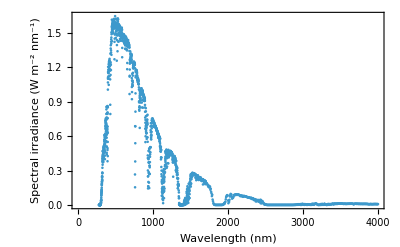

```mathematica
ListPlot[AM1p5global,Frame->True,FrameLabel->{"Wavelength (nm)","Spectral irradiance (W m^-2 nm^-1)"}]
```

```mathematica
(* Calculate the solar irradiance of the solar spectrum *)
(* units: W/m^2 *)
PowerofSun = Quiet[Integrate[Interpolation[AM1p5global][wl],{wl,AM1p5global[[1,1]],AM1p5global[[-1,1]]}]]
```

1000.38

```mathematica
(* Function to calculate the flux of a solar spectrum *)
(* units: A/(m^2 eV) *)
makeFlux[data_]:={fac/#[[1]],h c/(fac/#[[1]])^2 #[[1]]/(h c) #[[2]]}&/@data;
```

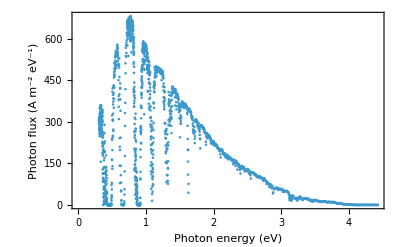

```mathematica
ListPlot[makeFlux[AM1p5global],Frame->True,FrameLabel->{"Photon energy (eV)","Photon flux (A m^-2 eV^-1)"}]
```

```mathematica
(* Photon flux at a certain photon energy *)
(* units: A/(m^2 eV) *)
Γ[En_]:=Interpolation[makeFlux[AM1p5global]][En];
```

## Silicon solar cell

The Si solar cell is modeled by fitting the current-voltage characteristics of a 27.4% efficient heterojunction interdigitated back-contact Silicon solar cell. The EQE of the Si solar cell is used to account for optical losses and parasitic absorption. The data for the JV curve and for the EQE are from M. A. Green  et al. Solar Cell Efficiency Tables (Version 67). Prog. Photovoltaics Res. Appl. 2026, 34, 482-496, DOI: https://doi.org/10.1002/pip.70068.

Functions

```mathematica
(* Temperature dependent intrinsic charge carrier concentration from K. Misiakos, et al. Accurate Measurements of the Silicon Intrinsic Carrier Density from 78 to 340 K. J.Appl.Phys. 1993, 74, 3293–3297 DOI:10.1063/1.354551 *)
(* units: m^-3 *)
Sini[T_] := 5.29 10^19 (T/300.)^2.54 Exp[-6726./T]*10^6
```

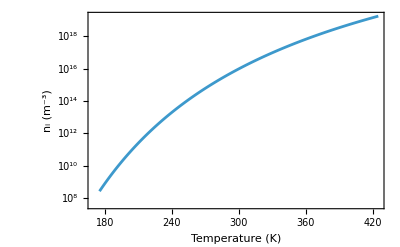

```mathematica
ListLogPlot[Table[{T,Sini[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","n_i (m^-3)"}]
```

```mathematica
(* Temperature dependent bandgap is calculated using Varshni’s empirical equation with values from the book Physics of Semiconductor Devices Physics of Semiconductor Devices, Wiley-Interscience, 1995 from Sze *)
(* units: eV *)
SiBandgap[T_] := 1.17 - 4.73 10^-4 T^2./(T+636.)
```

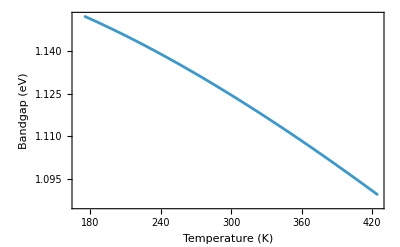

```mathematica
ListPlot[Table[{T,SiBandgap[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","Bandgap (eV)"}]
```

```mathematica
(* Temperature dependent Auger coefficient from J. Dziewior et al. Auger Coefficients for Highly Doped and Highly Excited Silicon. Appl.Phys.Lett. 1977, 346, 11–14 DOI:10.1063/1.89694 *)
(* units: 10^43 m^6/s *)
SiC[T_] :=6.89*10^-43*(T/300.)^(1./2.)
```

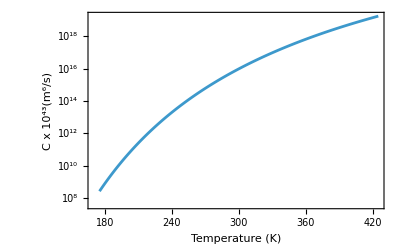

```mathematica
ListLogPlot[Table[{T,Sini[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","C x 10^43(m^6/s)"}]
```

Import JV and EQE

To account for spectral regions outside the published range, the regions below 300 and above 1200 nm were set to 0 % EQE.

```mathematica
(* Import JV characteristic*)
RecordSi = Import[NotebookDirectory[] <> "Input/IV-HTIBC-Si.csv"];
```

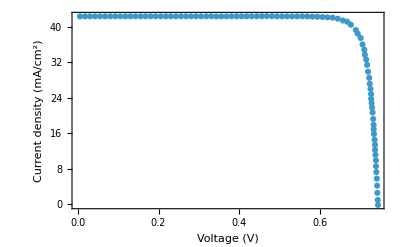

```mathematica
ListPlot[RecordSi,Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"}]
```

```mathematica
(* Import EQE *)
RecordSiEQE = Import[NotebookDirectory[] <> "Input/EQE-HTIBC-Si.csv"];
EQESi = Interpolation[RecordSiEQE,InterpolationOrder->1];
```

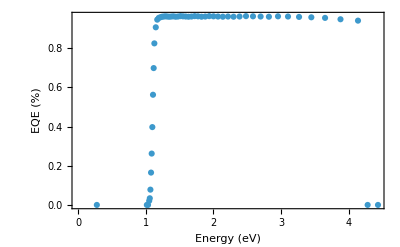

```mathematica
ListPlot[RecordSiEQE,Frame->True,FrameLabel->{"Energy (eV)","EQE (%)"}]
```

Current densities

```mathematica
(* Generation current density *)
jgSi = Quiet[NIntegrate[ EQESi[En] Γ[En],{En,0.8,4.4}]];
```

```mathematica
(* Radiative recombination current density *)
JRad0Si = q 2 Pi/(c^2 h2^3)NIntegrate[  En^2/(Exp[En/( k T)]-1),{En,SiBandgap[T],4.4}];
JRSi[V_,Il_,Rs_]:=JRad0Si ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
```

```mathematica
(* Auger recombination current density *)
JRAuger[V_,Il_,Rs_] :=  q L SiC[T] Sini[T]^3( Exp[(3 (V+Il*Rs*0.0001))/(2 k T)]-1);
```

```mathematica
(* Non-radiative recombination current density *)
JRnonSi[V_,Il_,Rs_] := 9.9*10^-43 Sini[T]^2(Exp[(V+Il*Rs*0.0001)/( k T)]-1);
```

```mathematica
(* Resistance *)
Resistance[V_,Il_,Rs_,Rsh_] := (V+Il *Rs*0.0001)/(Rsh*0.0001);
```

Silicon cell model

```mathematica
(* Thickness of Si *)
(* units: m *)
L =1.75*10^-4;
```

```mathematica
(* Parasitic resistances of Si cell *)
(* units: Ω cm^2 *)
RsSi = 0.01;
RshSi = 27000.;
```

```mathematica
(* Record Si Single-Junction *)
SQSi[Eg1_]:=Quiet[{

(* a = 0.01 pA/cm^2 *)
(* Rsh = 10000 ohm cm^2 *)
(* Rs = 0.08 ohm cm^2 *)
(* n = 1 *)

(* Make JV characteristic *)
dSi=Table[{v1,
FindRoot[
Il==jgSi-
JRSi[v1,Il,RsSi]-
JRAuger[v1,Il,RsSi]- 
JRnonSi[v1,Il,RsSi]-
Resistance[v1,Il,RsSi,RshSi]
,{Il,0}][[1,2]]},{v1,0,Eg1,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc *)
vocSi=FindRoot[ivSi[v],{v,Eg1-0.2}][[1,2]];

(* Calculate Jsc *)
jscSi=ivSi[0]/10;

(* Finding the maximum power conversion efficiency *)
NMaximize[{100ivSi[V] V/PowerofSun,0<V<Eg1},V]}][[1,1]];
```

Calculate efficiency

```mathematica
(* Model Si cell *)
"Efficiency: "<> ToString[Round[SQSi[SiBandgap[T]],0.01]] <>"%"
"Jsc: "<> ToString[Round[jscSi,0.01]]<> " mA/cm^2"
"Voc: "<> ToString[Round[vocSi,0.001]]<> " V"
"FF: "<> ToString[Round[N[NMaximize[{Interpolation[dSi][v] v,0<v<0.8},v][[1]]]/(jscSi*vocSi)*10,0.01]]<> "%"
```

Efficiency: 27.28%

Jsc: 42.34 mA/cm^2

Voc: 0.749 V

FF: 86.05%

```mathematica
devide[input_] := Table[{V,input[V]/10},{V,0,0.9,0.01}];
```

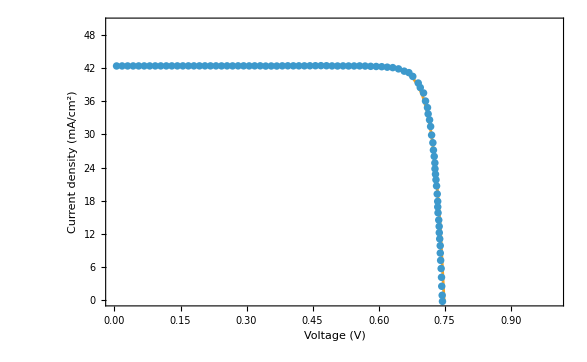

```mathematica
ListPlot[{RecordSi,ivSi//devide},Joined->{False,True},Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"},PlotRange->{{0,1.0},{0,50}}]
```

## QIBC Perovskite solar cell

The Perovskite solar cell is first numerically modeled using Silvaco TCAD, using  material parameters from experimental study using triple cation perovskite solar cell with a bandgap of 1.62 eV.

Functions

```mathematica
(* Temperature dependent bandgap from W. A. Saidi et al. Temperature Dependence of the Energy Levels of Methylammonium Lead Iodide Perovskite from First Principles. J.Phys.Chem.Lett. 2016, 7, 5247–5252 DOI:10.1021/acs.jpclett.6b02560.*)
(* units: eV *)
PerovskiteBandgap[T_] := 1.530555+ 0.0003*T
```

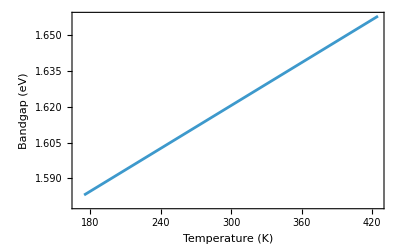

```mathematica
ListPlot[Table[{T,PerovskiteBandgap[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","Bandgap (eV)"}]
```

```mathematica
(* The temperature dependent intrinsic charge carrier concentration is calculated assuming that the dinsity of states in the conduction band and in the valance band at 25 °C are Subscript[N, C]=Subscript[N, V]=3.97 10^18 cm^-3. *)
(* units: m^-3 *)
Perovskiteni[T_]  := 6.02*^20*T^(3/2)*Exp[-PerovskiteBandgap[T]/(2 k T)]
```

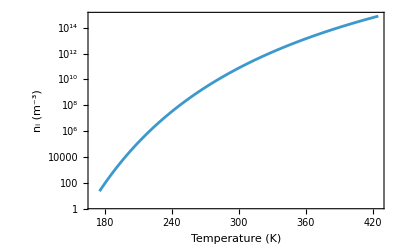

```mathematica
ListLogPlot[Table[{T,Perovskiteni[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","n_i (m^-3)"}]
```

```mathematica
(* Temperature deendent built-in bias *)
(* units: V *)
PerovskiteVbi[T_] := (k2 T)/q *Log[E,3.74629*^45/Perovskiteni[T]^2]
```

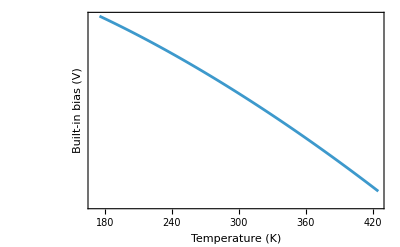

```mathematica
ListLogPlot[Table[{T,PerovskiteVbi[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","Built-in bias (V)"}]
```

```mathematica
(* The intensity dependent charge carrier lifetime is obtained by fitting experimental data from D. W. DeQuilettes et al.Impact of Microstructure on Local Carrier Lifetime in Perovskite Solar Cells.Science 2015, 348, 683–686 DOI:10.1126/science.aaa5333.*)
(* units: μs *)
PerovskiteT[Irradiation_]  :=2.63041*Irradiation^(-0.14)
```

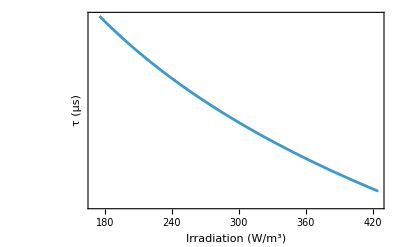

```mathematica
ListLogPlot[Table[{T,PerovskiteT[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Irradiation (W/m^3)","τ (μs)"}]
```

Import JV and EQE

To account for spectral regions outside the published range, the regions below 300 and above 900 nm were set to 0 % EQE.

```mathematica
(* Import JV characteristic*)
RecordPerovskiteForward = Import[NotebookDirectory[] <> "Input/JV-Ideal-1.62.csv"];
```

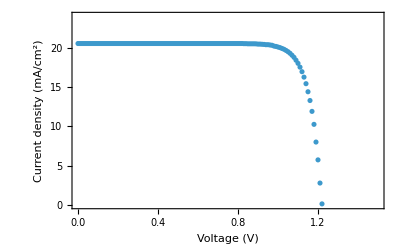

```mathematica
ListPlot[{RecordPerovskiteForward},PlotRange->{{0,1.5},{0,24}},Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"}]
```

```mathematica
(* Import EQE *)
RecordPerovskiteEQE = Import[NotebookDirectory[] <> "Input/EQE-ideal-1.62.csv"];
EQEPerovskite = Interpolation[RecordPerovskiteEQE,InterpolationOrder->1];
```

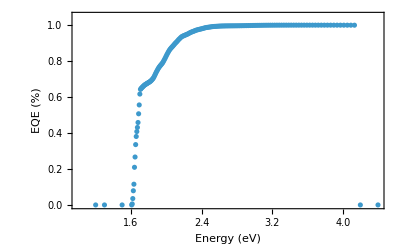

```mathematica
ListPlot[EQEPerovskite,PlotRange->{{1,4.4},{0,1.05}},Frame->True,FrameLabel->{"Energy (eV)","EQE (%)"}]
```

Current densities

```mathematica
(* Generation current density *)
jgPerovskite = Quiet[NIntegrate[ EQEPerovskite[En] Γ[En],{En,0,4.4}]];
```

```mathematica
(* Radiative recombination current density *)
JRad0Perovskite = q 2 Pi/(c^2 h2^3)NIntegrate[  En^2/(Exp[En/( k T)]-1),{En,PerovskiteBandgap[T],4.4}];
JRPerovskite[V_,Il_,Rs_]:=JRad0Perovskite ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
```

```mathematica
(* Non-radiative recombination current density *)
JRnonPerovskite[V_,Il_,Rs_] :=1.39*10^-25  Perovskiteni[T] Re[Sqrt[(PerovskiteVbi[T]-V)]]/PerovskiteT[PowerofSun](Exp[(V+Il*Rs*0.0001)/(2 k T)]-1);
```

```mathematica
(* Resistance *)
Resistance[V_,Il_,Rs_,Rsh_] := (V+Il *Rs*0.0001)/(Rsh*0.0001);
```

Perovskite cell model

```mathematica
(* Parasitic resistances of perovskite cell *)
(* units: Ω cm^2 *)
RsPerovskite = 0.001;
RshPerovskite = 100000.;
```

```mathematica
(* Record Perovskite Single-Junction *)
SQPerovskite[Eg1_]:=Quiet[{

(* a = 28.5 pA/cm^2 *)
(* Rsh = 1500 ohm cm^2 *)
(* Rs = 3.10 ohm cm^2 *)
(* n = 2.0 *)

(* Make JV characteristic *)
dPerovskite=Table[{v1,FindRoot[Il==jgPerovskite-
JRPerovskite[v1,Il,RsPerovskite]-
JRnonPerovskite[v1,Il,RsPerovskite]-
Resistance[v1,Il,RsPerovskite,RshPerovskite]
,{Il,0}][[1,2]]},{v1,0,Eg1,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc *)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg1-0.2}][[1,2]];

(* Calculate Jsc *)
jscPerovskite=ivPerovskite[0]/10;

(* Finding the maximum power conversion efficiency *)
NMaximize[{100ivPerovskite[V] V/PowerofSun,0<V<Eg1},V]}][[1,1]];
```

Calculate efficiency

```mathematica
(* Model perovskite cell *)
"Efficiency: "<> ToString[Round[SQPerovskite[PerovskiteBandgap[T]],0.001]] <>"%"
"Jsc: "<> ToString[Round[jscPerovskite,0.001]]<> " mA/cm^2"
"Voc: "<> ToString[Round[vocPerovskite,0.010]]<> " V"
"FF: "<> ToString[Round[N[NMaximize[{Interpolation[dPerovskite][v] v,0<v<1},v][[1]]]/(jscPerovskite*vocPerovskite)*10,0.001]]<> "%"
```

Efficiency: 24.849%

Jsc: 20.475 mA/cm^2

Voc: 1.34 V

FF: 74.584%

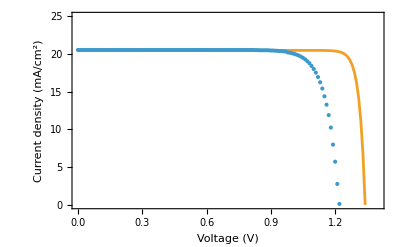

```mathematica
(*Extend the voltage range to 1.3 V*)
devide[input_]:=Table[{V,input[V]/10},{V,0,1.4,0.01}];
(*Plot with axes limits*)
ListPlot[{RecordPerovskiteForward,ivPerovskite//devide},Joined->{False,True,True},Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"},PlotRange->{{0,1.4},{0,25}}]
```

## Perovskite/silicon tandem solar cell

Optical model

Optical losses are included by fitting a Gaussian distribution to the onset of the perovskite EQE. 10 % of the light with an energy below the Gaussian distribution is assumed to be absorbed by parasitic absorption. A small fraction of light between the bandgap and 600 nm that is transmitted is included to follow published transmission curves such as from B. Chen et al. Efficient Semitransparent Perovskite Solar Cells for 23.0%-Efficiency Perovskite/Silicon Four-Terminal Tandem Cells. Adv. Energy Mater. 2016, 6, 1601128 DOI: 10.1002/aenm.201601128.

```mathematica
(* Fit Gaussian *)
model[x_]=0.0876Evaluate[PDF[NormalDistribution[x0,sigma],x]];
data = Table[{i,EQEPerovskite[i]},{i,1.45,1.75,0.01}];
fit=FindFit[data,model[x],{x0,sigma},x];
gam=0.;
```

```mathematica
(* Transmitted light to silicon bottom cell *)
TransmittedtoSi = Interpolation[Join[Table[{x,gam+model[x]/.fit},{x,0.8,1.70,0.01}],Table[{i,Fit[{{1.70,gam+model[1.70]/. fit},{2,1}},{1,x},x]/.x->i},{i,1.71,2,0.01}],Table[{x,1},{x,2.01,4,0.01}]],InterpolationOrder->1];
```

```mathematica
(* EQE of Si back cell *)
EQESiback =Interpolation[Replace[Table[{x,EQESi[x]-TransmittedtoSi[x]},{x,0.8,4,0.01}],n_?(#<0&)->0,{2}],InterpolationOrder->1];
```

```mathematica
Backtowavelangth[data_] := Table[{fac/wl,data[wl]},{wl,0.8,4,0.01}];
```

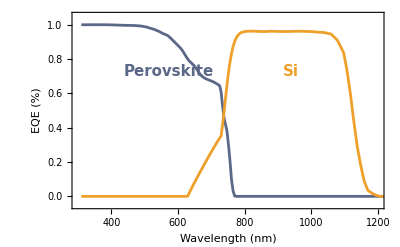

```mathematica
Quiet[Show[ListPlot[{EQEPerovskite//Backtowavelangth,EQESiback//Backtowavelangth},Joined->{True,True,True},Frame->True,FrameLabel->{"Wavelength (nm)","EQE (%)"},
PlotStyle->{ColorData[10,8],ColorData[10,3],GrayLevel[0.5]},
PlotRange->{{300,1200},{-0.05,1.05}}],

Epilog->{
Inset[Style["Perovskite",ColorData[10,8],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.31,0.70}]],
Inset[Style["Si",ColorData[10,3],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.70,0.7}]]
}]]
```

```mathematica
(* Optical thickness of perovskite top cell. This value has to be optimized in order to current-match the silicon bottom cell with the perovskite top cell *)
thick= 1.1;
```

```mathematica
(* Transmitted light to silicon bottom cell when using an optically-thin perovskite top cell *)
TransmittedtoSithin = Interpolation[Join[Table[{x,gam+thick*(model[x]/.fit)},{x,0.8,1.70,0.01}],Table[{i,(Fit[{{1.70,gam+model[1.70]/. fit},{2,1}},{1,x},x]/.x->i)*thick},{i,2.1,2,0.01}],Table[{x,thick*1},{x,2.1,4,0.01}]],InterpolationOrder->1];
```

```mathematica
(* EQE of Si back cell when using an optically-thin perovskite top cell *)
EQESibackthin =Interpolation[Replace[Table[{x,EQESi[x]-TransmittedtoSithin[x]},{x,0.8,4,0.01}],n_?(#<0&)->0,{2}],InterpolationOrder->1];
```

```mathematica
(* EQE of optically-thin perovskite top cell *)
EQEPerovskitethin =Interpolation[Table[{x,EQEPerovskite[x]*thick},{x,0.8,4,0.01}],InterpolationOrder->1];
```

```mathematica
plottransmited = Interpolation[Table[{x,1-1*TransmittedtoSi[x]},{x,0.8,4,0.01}]];
```

```mathematica
plottransmitedthin = Interpolation[Table[{x,1-1*TransmittedtoSithin[x]},{x,0.8,4,0.01}]];
```

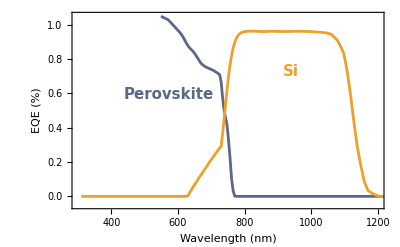

```mathematica
Quiet[Show[ListPlot[{EQEPerovskitethin//Backtowavelangth,EQESibackthin//Backtowavelangth},Joined->True,Frame->True,FrameLabel->{"Wavelength (nm)","EQE (%)"},
PlotStyle->{ColorData[10,8],ColorData[10,3],GrayLevel[0.5]},PlotRange->{{300,1200},{-0.05,1.05}}],

Epilog->{
Inset[Style["Perovskite",ColorData[10,8],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.31,0.58}]],
Inset[Style["Si",ColorData[10,3],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.70,0.7}]]}]]
```

Current densities

```mathematica
(* Calculate generation current densities *)
jgPerovskitetandem =Quiet[ NIntegrate[EQEPerovskite[En] Γ[En],{En,1.2,4.4}]];
jgSitandem =Quiet[ NIntegrate[EQESiback[En] Γ[En],{En,0.8,3.5}]];
```

```mathematica
(* Calculate generation current densities for optical thin perovskite *)
jgPerovskitetandemthin = Quiet[ NIntegrate[ EQEPerovskitethin[En] Γ[En],{En,1.2,4.4}]];
jgSitandemthin = Quiet[ NIntegrate[ EQESibackthin[En] Γ[En],{En,0.8,3.5}]];
```

```mathematica
(* Radiative recombination current densities *)
JRPerovskite[V_,Il_,fg_,Rs_]:=fg JRad0Perovskite ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
JRSi[V_,Il_,fg_,Rs_]:=fg JRad0Si ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
```

```mathematica
(* Resistance *)
Resistance[V_,Il_,Rs_,Rsh_] := (V+Il *Rs*0.0001)/(Rsh*0.0001);
```

Tandem solar cell model

To model the tandem solar cells we assume a perfect reflector on the back side of the silicon bottom cell and no selective reflector between the perovskite top cell and the Si bottom cell.For simplicity we neglect reabsorption of luminescence between the two subcells.

### Current-matched series tandem

```mathematica
(* Realistic series tandem Limit *)
SQSeries[Eg1_,Eg2_]:=Quiet[{

(* Make JV characteristic of Si bottom cell *)
dSi=Table[{v1,
FindRoot[
Il1==jgSitandemthin-
JRSi[v1,Il1,1,RsSi]-
JRAuger[v1,Il1,RsSi]- 
JRnonSi[v1,Il1,RsSi]-
Resistance[v1,Il1,RsSi,RshSi]
,{Il1,0}][[1,2]]},{v1,0,Eg1-0.1,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc and Jsc of Si bottom cell*)
vocSi=FindRoot[ivSi[v],{v,Eg1-0.2}][[1,2]];
jscSi = ivSi[0];

(* Make JV characteristic of perovskite top cell*)
dPerovskite=Table[{v2,
FindRoot[
Il2==jgPerovskitetandemthin-
JRPerovskite[v2,Il2,2,RsPerovskite]-
JRnonPerovskite[v2,Il2,RsPerovskite]-
Resistance[v2,Il2,RsPerovskite,RshPerovskite]
,{Il2,0}][[1,2]]},{v2,0,Eg2-0.2,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc and Jsc of perovskite top cell*)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg2-0.3}][[1,2]];
jscPerovskite = ivPerovskite[0];

ivCurve={};

(* Make series tandem JV characteristic *)
Do[{
d=Table[{v1,(ivSi[v1]-ivPerovskite[v2])^2},{v1,0,vocSi,.001}];
v1=Cases[d,{_,Min@d[[All,2]]}][[1,1]];AppendTo[ivCurve,{v1+v2,Min[ivPerovskite[v2],ivSi[v1]]}];Clear[v1]},{v2,0,vocPerovskite,.001}]

(* Finding the maximum power conversion efficiency *)
NMaximize[{100 Interpolation[ivCurve][V] V/PowerofSun,First[ivCurve][[1]]<V<Last[ivCurve][[1]]},V][[1]]}][[1,1]];
```

### Voltage-matched module tandem

```mathematica
(* Realistic module tandem limit *)
SQModule[Eg1_,Eg2_,n_]:=Quiet[{
(* n.. number of bottom cells for each top cell *)

(* Make JV characteristic of Si bottom cell *)
dSi=Table[{v1,
FindRoot[
Il1==(jgSitandem-
JRSi[v1/n,Il1,1,RsSi]-
JRAuger[v1/n,Il1,RsSi]- 
JRnonSi[v1/n,Il1,RsSi]-
Resistance[v1/n,Il1,RsSi,RshSi])/n
,{Il1,0}][[1,2]]},{v1,0,(Eg1-0.1)*n,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc and Jsc of Si bottom cell*)
vocSi=FindRoot[ivSi[v],{v,(Eg1-0.2)*n}][[1,2]];
jscSi = ivSi[0];

(* Make JV characteristic of perovskite top cell*)
dPerovskite=Table[{v2,
FindRoot[
Il2==jgPerovskitetandem-
JRPerovskite[v2,Il2,2,RsPerovskite]-
JRnonPerovskite[v2,Il2,RsPerovskite]-
Resistance[v2,Il2,RsPerovskite,RshPerovskite]
,{Il2,0}][[1,2]]},{v2,0,Eg2-0.2,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc and Jsc of perovskite top cell*)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg2-0.3}][[1,2]];
jscPerovskite = ivPerovskite[0];

(* Make JV-characteristic of module tandem *)
d = Table[{v,Interpolation[dSi][v]+Interpolation[dPerovskite][v]},{v,0,Eg2-0.2,0.001}];
iv=Interpolation[d];

(* Calculate Voc and Jsc of module tandem *)
voc=FindRoot[iv[v],{v,Eg2-0.3}][[1,2]];

(* Finding the maximum power conversion efficiency *)
NMaximize[{100 iv[V] V/PowerofSun,0 <V<voc},V][[1]]}][[1]];
```

```mathematica
Four-terminal tandem
```

Four-tandem terminal

```mathematica
(*Three-terminal tandem*)(*Rz:additional shared-terminal resistance in ohm cm^2. Current densities:A/m^2,as in the original notebook.Perovskite negative is connected to silicon positive.Two independently controlled electrical outputs are assumed.*)
ClearAll[SQThree];

SQThree[Eg1_?NumericQ,Eg2_?NumericQ,Rz_:0.]:=Module[{fSi,fPe,vocSi3,vocPe3,dSi3,dPe3,ivSi3,ivPe3,jSi,jPe,power3,r,v,j,vp,vs,solution},(*Check that the existing model inputs are available*)If[!And@@(NumericQ/@{PowerofSun,jgSitandem,jgPerovskitetandem,Rz})||!TrueQ[PowerofSun>0&&jgSitandem>0&&jgPerovskitetandem>0&&Rz>=0],Return[$Failed]];
(*Silicon current-balance equation*)fSi[v_?NumericQ,j_?NumericQ]:=j-jgSitandem+JRSi[v,j,1,RsSi]+JRAuger[v,j,RsSi]+JRnonSi[v,j,RsSi]+Resistance[v,j,RsSi,RshSi];
(*Perovskite current-balance equation*)fPe[v_?NumericQ,j_?NumericQ]:=j-jgPerovskitetandem+JRPerovskite[v,j,2,RsPerovskite]+JRnonPerovskite[v,j,RsPerovskite]+Resistance[v,j,RsPerovskite,RshPerovskite];
(*Calculate individual subcell open-circuit voltages*)vocSi3=v/. FindRoot[fSi[v,0.]==0,{v,0.,N[Eg1]},Method->"Brent"];
vocPe3=v/. FindRoot[fPe[v,0.]==0,{v,0.,N[Eg2]},Method->"Brent"];
(*Make JV characteristic of the silicon bottom cell*)dSi3=Append[Table[{v,j/. FindRoot[fSi[v,j]==0,{j,0.,N[jgSitandem]},Method->"Brent"]},{v,Most[Subdivide[0.,vocSi3,Ceiling[vocSi3/0.001]]]}],{vocSi3,0.}];
(*Make JV characteristic of the perovskite top cell*)dPe3=Append[Table[{v,j/. FindRoot[fPe[v,j]==0,{j,0.,N[jgPerovskitetandem]},Method->"Brent"]},{v,Most[Subdivide[0.,vocPe3,Ceiling[vocPe3/0.001]]]}],{vocPe3,0.}];
ivSi3=Interpolation[dSi3,InterpolationOrder->1];
ivPe3=Interpolation[dPe3,InterpolationOrder->1];
jSi[v_?NumericQ]:=ivSi3[Clip[v,{0.,vocSi3}]];
jPe[v_?NumericQ]:=ivPe3[Clip[v,{0.,vocPe3}]];
(*Convert ohm cm^2 to ohm m^2*)r=Rz*0.0001;
(*Total extracted power density.vp and vs are subcell voltages before the added Rz drop.The shared lead carries the difference of subcell currents.*)power3[vp_?NumericQ,vs_?NumericQ]:=vp*jPe[vp]+vs*jSi[vs]-r*(jPe[vp]-jSi[vs])^2;
(*Maximize total efficiency.Both external output-port voltages must be nonnegative.*)solution=NMaximize[{100*power3[vp,vs]/PowerofSun,0<=vp<=vocPe3&&0<=vs<=vocSi3&&vp-r*(jPe[vp]-jSi[vs])>=0&&vs+r*(jPe[vp]-jSi[vs])>=0},{vp,vs},Method->{"DifferentialEvolution","RandomSeed"->17},MaxIterations->2000,AccuracyGoal->8,PrecisionGoal->7];
solution[[1]]];
```

### Four-terminal tandem

```mathematica
(* Realistic four-terminal tandem limit *)
SQFour[Eg1_,Eg2_]:=Quiet[{

(* Make JV characteristic of Si bottom cell *)
dSi=Table[{v1,
FindRoot[
Il1==jgSitandem-
JRSi[v1,Il1,1,RsSi]-
JRAuger[v1,Il1,RsSi]- 
JRnonSi[v1,Il1,RsSi]-
Resistance[v1,Il1,RsSi,RshSi]
,{Il1,0}][[1,2]]},{v1,0,Eg1-0.1,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc and Jsc of Si bottom cell*)
vocSi=FindRoot[ivSi[v],{v,Eg1-0.2}][[1,2]];
jscSi = ivSi[0];

(* Make JV characteristic of perovskite top cell*)
dPerovskite=Table[{v2,
FindRoot[
Il2==jgPerovskitetandem-
JRPerovskite[v2,Il2,2,RsPerovskite]-
JRnonPerovskite[v2,Il2,RsPerovskite]-
Resistance[v2,Il2,RsPerovskite,RshPerovskite]
,{Il2,0}][[1,2]]},{v2,0,Eg2-0.2,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc and Jsc of perovskite top cell*)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg2-0.3}][[1,2]];
jscPerovskite = ivPerovskite[0];

(* Finding the maximum power conversion efficiency *)
NMaximize[{100 ivSi[V] V/PowerofSun,0<V<vocSi},V][[1]]+NMaximize[{100 ivPerovskite[V] V/PowerofSun,0 <V<vocPerovskite},V][[1]]}][[1]];
```

Calculate efficiencies

```mathematica
(* Model perovskite/Si tandem solar cells *)
"Series tandem: "<> ToString[Round[SQSeries[SiBandgap[T],PerovskiteBandgap[T]],0.001]] <>"%"
"Module tandem: "<> ToString[Round[SQModule[SiBandgap[T],PerovskiteBandgap[T],1.],0.001]] <>"%"
(*Additional shared-terminal resistance,in ohm cm^2*)
Rz3T=0.;
"Three-terminal tandem: "<>ToString[Round[SQThree[SiBandgap[T],PerovskiteBandgap[T],Rz3T],0.001]]<>"%"
"Four-terminal tandem: "<> ToString[Round[SQFour[SiBandgap[T],PerovskiteBandgap[T]],0.001]] <>"%"
```

Series tandem: 38.838%

Module tandem: 26.829%

Three-terminal tandem: 37.787%

Four-terminal tandem: 37.787%

```mathematica
(* ONE BLOCK: CALCULATE J-V CURVES, DISPLAY PLOTS/TABLES, EXPORT EVERYTHING.
   Replace the earlier generated J-V/table/display extensions with this file.
   Keep and evaluate your original physical-model and input-data cells first.
   This file includes all generated helpers; it does not load other code files.
*)

(* USER SETTINGS -- only change the output folder here.
   Automatic: Tandem_JV_Exports beside this .wl file (Get), or saved notebook
   (pasted Input cell). Unsaved notebooks fall back to Documents/Codex.
   For an explicit folder, use: tandemOutputRoot = "D:/Tandem Results";
*)
tandemOutputRoot = Automatic;

(* These are the defaults from the supplied baseline. Copy your own current
   n and resistance settings here if you have changed them in your model. *)
tandemJVSettings = {
  "n"->1.88, "Rz3T"->0., "Points"->1200,
  "SeriesOptics"->"NotebookThin",
  "Radd2T"->0., "RaddVMMTop"->0., "RaddVMMBottomString"->0.,
  "RaddVMMBus"->0., "Radd4TTop"->0., "Radd4TBottom"->0.
};
tandemFigureFormats = {"PNG","SVG"}; (* Use {} for CSV files only. *)

(* Capture the current source location before any export calls. *)
tandemSourceFolder = If[StringQ[$InputFileName] && StringLength[$InputFileName]>0,
  DirectoryName[ExpandFileName[$InputFileName]],
  Quiet[Check[NotebookDirectory[],$Failed]]];
(* J-V ONLY: COMPLETE REPLACEMENT for the previous MakeTandemJVPlots,
   ExportTandemJV and RUN block. Paste after the original physical-model cells.
   The RUN section calculates four device J-V plots AND AUTOMATICALLY EXPORTS
   CSV files. No power-density plots or assumed converter outputs are included.

   Circuit scope: series 2T; parallel voltage-matched module; common-Z s-type
   3T made from two 2-terminal subcells joined by a shared lead; independent 4T.
   This is a lumped equivalent-circuit calculation using your existing subcell
   equations, not a validation of their fitted parameters or a general 3-contact
   IBC transport model. Original subcell and SQ... definitions are not changed.

   Internal currents: A/m^2. Exported and plotted currents: mA/cm^2 (multiply by 0.1).
   Added resistances: ohm cm^2 of common aperture (multiply by 10^-4 internally).
   2T low-voltage extension continues the supplied equations into reverse bias
   without avalanche/breakdown. Affected points are marked in the diagnostic CSV.
   VMM uses Jlocal = n Jstring, including in every bottom-cell resistance term.
   3T has two output ports, with the other external port fixed at its joint-MPP
   voltage during each sweep. 4T has two independent outputs. Neither has a
   unique intrinsic overall J-V curve, so no artificial total current is plotted.

   Physics/reporting reference: Warren et al., ACS Energy Lett. 2020,
   https://doi.org/10.1021/acsenergylett.0c00068
   Export reference: https://reference.wolfram.com/language/ref/format/CSV.html
*)

ClearAll[MakeTandemJVPlots];
Options[MakeTandemJVPlots] = {
  "n" -> 1.88, "Rz3T" -> 0., "Points" -> 1200,
  "SeriesOptics" -> "NotebookThin",
  "Radd2T" -> 0.,
  "RaddVMMTop" -> 0., "RaddVMMBottomString" -> 0., "RaddVMMBus" -> 0.,
  "Radd4TTop" -> 0., "Radd4TBottom" -> 0.
};

MakeTandemJVPlots[OptionsPattern[]] := Catch[Module[
  {n = N[OptionValue["n"]], rz = N[OptionValue["Rz3T"]],
   pts = OptionValue["Points"], optics = OptionValue["SeriesOptics"],
   r2, rmt, rms, rmb, r4t, r4s, egS, egP, pe, si, pe2, si2,
   pm, sm, p4, s4, root, build, fromData, lead, jof,
   maximize1, mpp, sol2, rowsM, vMoc, jM,
   gp2, gs2, fPe2, fSi2, voc2, oldJ2, oldVp2, grid2, solve2, rr2, iv2, metrics2, vs2,
   solM, mp4P, mp4S, pThree, ports, sol3, vp3, vs3, port3,
   rows3P, rows3S, cut, fig2, figM, fig3, fig4, figure,
   summary, table, data, v, j, a, b, dv, u, jp, js, vs, vp,
   colors, checkInputs, j3p, j3s, pmax4, scaleJV, plotJV,
   rows2JV, rowsMJV, rows3Top, rows3Bottom, rows4Top, rows4Bottom,
   row3, plots, tables, warnings, x, y, headers3,
   summaryRows, settings, xyTable,plotCSV,diagnostics},

  {r2,rmt,rms,rmb,r4t,r4s} = 10^-4 N[OptionValue[#]& /@
    {"Radd2T","RaddVMMTop","RaddVMMBottomString","RaddVMMBus",
     "Radd4TTop","Radd4TBottom"}];
  checkInputs = {PowerofSun,jgSitandem,jgPerovskitetandem,RsSi,
    RsPerovskite,RshSi,RshPerovskite,T,n,rz,r2,rmt,rms,rmb,r4t,r4s};
  If[!VectorQ[checkInputs, NumericQ] ||
    !TrueQ[PowerofSun>0 && jgSitandem>0 && jgPerovskitetandem>0 &&
      n>0 && Min[{rz,r2,rmt,rms,rmb,r4t,r4s}]>=0] ||
    !IntegerQ[pts] || pts<100 ||
    !MemberQ[{"NotebookThin","SameAsOtherTandems"},optics],
    Throw[Failure["Inputs",<|"MessageTemplate" ->
      "Evaluate the original tandem input cells first. Use nonnegative added resistances, n>0, and Points>=100."|>],"PV"]];
  egS=N[SiBandgap[T]]; egP=N[PerovskiteBandgap[T]];

  (* Bracketed roots: stop on a failure rather than silently plot bad data. *)
  root[fun_,lo_,hi_] := Module[{fl=N[fun[lo]],fh=N[fun[hi]],z,ans},
    If[!VectorQ[{fl,fh},NumericQ],
      Throw[Failure["RootNumeric",<|"MessageTemplate"->
        "The JV equation did not return numerical residuals."|>],"PV"]];
    If[Abs[fl]<10^-10,Return[N[lo]]];
    If[Abs[fh]<10^-10,Return[N[hi]]];
    If[!TrueQ[fl fh<=0],
      Throw[Failure["RootBracket",<|"MessageTemplate"->
        "A root was not bracketed. Check the input JV model and its validity range.",
        "Bracket"->{lo,hi},"Residuals"->{fl,fh}|>],"PV"]];
    ans=Check[z /. FindRoot[fun[z]==0,{z,N[lo],N[hi]},
      Method->"Brent",Compiled->False,AccuracyGoal->10,PrecisionGoal->9],$Failed];
    If[!NumericQ[ans],Throw[Failure["Root",<|"MessageTemplate"->
      "A JV root did not converge."|>],"PV"]];ans];

  fromData[d_,voc_] := Module[{iv,forward,inv},
    iv=Interpolation[SortBy[d,First],InterpolationOrder->1];
    forward=SortBy[Join[{{0.,iv[0.]}},
      Select[d,0.<#[[1]]<voc && #[[2]]>0.&],{{N[voc],0.}}],First];
    inv=Interpolation[SortBy[Reverse /@ forward,First],InterpolationOrder->1];
    <|"Data"->d,"Forward"->forward,"J"->iv,"V"->inv,
      "Voc"->N[voc],"Jsc"->iv[0.]|>];

  build[type_,g_,eg_,vmax_:Automatic] := Module[
    {f,current,voc,hi,lo,upper,grid,d,z},
    f[x_?NumericQ,y_?NumericQ] := If[type=="Pe",
      y-g+JRPerovskite[x,y,2,RsPerovskite]+
        JRnonPerovskite[x,y,RsPerovskite]+
        Resistance[x,y,RsPerovskite,RshPerovskite],
      y-g+JRSi[x,y,1,RsSi]+JRAuger[x,y,RsSi]+JRnonSi[x,y,RsSi]+
        Resistance[x,y,RsSi,RshSi]];
    voc=root[Function[z,f[z,0.]],0.,eg];
    hi=If[vmax===Automatic,voc,Max[voc,N[vmax]]];
    current[x_?NumericQ] := Module[{low=-N[g],high=1.01 N[g]+1.,count=0},
      While[TrueQ[f[x,low]>0] && count<40,low=2 low;count++];
      root[Function[z,f[x,z]],low,high]];
    grid=Sort[DeleteDuplicates[Join[N[Subdivide[0.,hi,pts]],{voc}]]];
    d=({#,If[#==voc,0.,current[#]]}& /@ grid);
    fromData[d,voc]];

  (* Change the voltage/current scale first; then add an EXTERNAL lead loss. *)
  lead[cur_,r_,nv_:1.,nj_:1.] := Module[{d},
    d=({nv #[[1]]-r nj #[[2]],nj #[[2]]}& /@ cur["Data"]);
    fromData[d,nv cur["Voc"]]];
  jof[cur_,x_?NumericQ] := cur["J"][Clip[x,{0.,cur["Voc"]}]];
  maximize1[fun_,hi_] := Module[{z,sol},
    sol=NMaximize[{fun[z],0<=z<=hi},z,
      Method->{"DifferentialEvolution","RandomSeed"->17},
      MaxIterations->1500,AccuracyGoal->8,PrecisionGoal->7];
    {N[z/.sol[[2]]],N[sol[[1]]]}];
  mpp[cur_] := maximize1[Function[z,z jof[cur,z]],cur["Voc"]];

  pe=build["Pe",jgPerovskitetandem,egP];
  si=build["Si",jgSitandem,egS];

  (* SERIES 2T: use one common current; add voltages at THAT current. *)
  If[optics=="NotebookThin",
    If[!VectorQ[{jgSitandemthin,jgPerovskitetandemthin},NumericQ],
      Throw[Failure["ThinInputs",<|"MessageTemplate"->
        "Evaluate the thin-top optical generation currents first."|>],"PV"]];
    pe2=build["Pe",jgPerovskitetandemthin,egP];
    si2=build["Si",jgSitandemthin,egS],pe2=pe;si2=si];
  (* FULL SERIES SWEEP: solve both current equations at each Vout.
     Vout = VPe + VSi - Radd2T*J (R converted to ohm m^2).
     Continue existing diode/recombination/shunt equations below zero
     subcell voltage. No avalanche/breakdown term is added or calibrated. *)
  {gp2,gs2}=N[If[optics=="NotebookThin",
    {jgPerovskitetandemthin,jgSitandemthin},
    {jgPerovskitetandem,jgSitandem}]];
  fPe2[x_?NumericQ,y_?NumericQ]:=y-gp2+
    JRPerovskite[x,y,2,RsPerovskite]+
    JRnonPerovskite[x,y,RsPerovskite]+
    Resistance[x,y,RsPerovskite,RshPerovskite];
  fSi2[x_?NumericQ,y_?NumericQ]:=y-gs2+JRSi[x,y,1,RsSi]+
    JRAuger[x,y,RsSi]+JRnonSi[x,y,RsSi]+Resistance[x,y,RsSi,RshSi];
  voc2=pe2["Voc"]+si2["Voc"];
  oldJ2=0.; oldVp2=pe2["Voc"];
  grid2=Reverse[N[Subdivide[0.,voc2,pts]]];
  rows2JV=Table[
    If[v==voc2,{oldJ2,oldVp2}={0.,pe2["Voc"]},
      solve2=Quiet[FindRoot[
        {fPe2[vp,j]==0,fSi2[v+r2 j-vp,j]==0},
        {{j,oldJ2},{vp,oldVp2}},Compiled->False,MaxIterations->100,
        AccuracyGoal->8,PrecisionGoal->7],{FindRoot::lstol}];
      If[!MatchQ[solve2,{__Rule}],
        Throw[Failure["SeriesRoot",<|"MessageTemplate"->
          "The coupled series solution failed; no incomplete curve is returned.",
          "Voltage_V"->v|>],"PV"]];
      {oldJ2,oldVp2}=N[{j,vp}/.solve2]];
    vs2=v+r2 oldJ2-oldVp2;
    rr2=Max[Abs[{fPe2[oldVp2,oldJ2],fSi2[vs2,oldJ2]}]];
    (* Accept a point only if BOTH subcell current equations are satisfied. *)
    If[!TrueQ[rr2<10^-6] || !TrueQ[oldJ2>=-10^-7],
      Throw[Failure["SeriesResidual",<|"MessageTemplate"->
        "A series point failed the current-balance check.",
        "Voltage_V"->v,"Residual_A_m2"->rr2|>],"PV"]];
    {v,0.1 oldJ2,oldVp2,vs2,r2 oldJ2,v oldJ2,
     If[Min[oldVp2,vs2]<-10^-9,1,0],rr2}, {v,grid2}];
  rows2JV=Reverse[rows2JV];
  iv2=Interpolation[rows2JV[[All,{1,2}]],InterpolationOrder->1];
  sol2=maximize1[Function[z,10 z iv2[z]],voc2];
  metrics2=<|"Jsc_mA_cm2"->rows2JV[[1,2]],"Voc_V"->voc2,
    "Vmp_V"->sol2[[1]],"Jmp_mA_cm2"->iv2[sol2[[1]]],
    "Pmax_W_m2"->sol2[[2]],"PCE_percent"->100 sol2[[2]]/PowerofSun,
    "FF_percent_model_extrapolation"->100 sol2[[2]]/(10 rows2JV[[1,2]] voc2),
    "VPe_at_tandem_short_circuit_V"->rows2JV[[1,3]],
    "VSi_at_tandem_short_circuit_V"->rows2JV[[1,4]],
    "Max_current_residual_A_m2"->Max[rows2JV[[All,8]]]|>;

  (* VMM: Si string V=n*vcell and J=Jcell/n, for a common aperture.
     Include signed branch current above each branch Voc. No extrapolation
     and no clipping of a negative/absorbing branch to zero are used here. *)
  vMoc=Max[pe["Voc"],n si["Voc"]];
  pm=lead[build["Pe",jgPerovskitetandem,egP,vMoc],rmt];
  sm=lead[build["Si",jgSitandem,egS,vMoc/n],rms,n,1./n];
  jM[x_?NumericQ] := pm["J"][Clip[x,{0.,vMoc}]]+
    sm["J"][Clip[x,{0.,vMoc}]];
  vMoc=root[jM,Min[pe["Voc"],n si["Voc"]],vMoc];
  a=If[rmb==0,0.,root[Function[z,z-rmb jM[z]],0.,vMoc]];
  solM=maximize1[Function[z,(z-rmb jM[z]) jM[z]],vMoc];
  (*Generate VMM curves up to the larger branch open-circuit voltage.Keep the combined VMM Voc and maximum-power point in the data.*)
rowsM=Table[jp=pm["J"][v];
js=sm["J"][v];
u=v-rmb (jp+js);
{u,v jp,v js,u (jp+js),v,jp,js},{v,Sort[DeleteDuplicates[Join[N[Subdivide[a,Max[pe["Voc"],n si["Voc"]],pts]],{vMoc,solM[[1]]}]]]}];

  (* FOUR TERMINALS: independent port maxima, with optional lead losses. *)
  p4=lead[pe,r4t];s4=lead[si,r4s];
  mp4P=mpp[p4];mp4S=mpp[s4];pmax4=mp4P[[2]]+mp4S[[2]];

  (* THREE TERMINALS: common-Z, s-type. The shared lead carries J_Si-J_Pe. *)
  j3p[x_?NumericQ] := jof[pe,x];
  j3s[x_?NumericQ] := jof[si,x];
  ports[x_?NumericQ,y_?NumericQ] := Module[{d=j3p[x]-j3s[y]},
    {x-10^-4 rz d,y+10^-4 rz d}];
  pThree[x_?NumericQ,y_?NumericQ] := x j3p[x]+y j3s[y]-
    10^-4 rz (j3p[x]-j3s[y])^2;
  sol3=NMaximize[{pThree[vp,vs],0<=vp<=pe["Voc"] &&
      0<=vs<=si["Voc"] &&
      vp-10^-4 rz (j3p[vp]-j3s[vs])>=0 &&
      vs+10^-4 rz (j3p[vp]-j3s[vs])>=0},
    {vp,vs},Method->{"DifferentialEvolution","RandomSeed"->17},
    MaxIterations->2500,AccuracyGoal->8,PrecisionGoal->7];
  {vp3,vs3}=N[{vp,vs}/.sol3[[2]]];port3=ports[vp3,vs3];
  (* Each cut fixes the OTHER EXTERNAL port voltage at the joint optimum. *)
  cut[which_] := Module[{grid,out={},x,y,f,lo,hi,pair},
    grid=Sort[DeleteDuplicates[Join[N[Subdivide[0.,
      If[which==1,pe["Voc"],si["Voc"]],pts]],{If[which==1,vp3,vs3]}]]];
    Do[
      If[which==1,
        x=z;f[w_?NumericQ]:=ports[x,w][[2]]-port3[[2]];hi=si["Voc"],
        y=z;f[w_?NumericQ]:=ports[w,y][[1]]-port3[[1]];hi=pe["Voc"]];
      If[TrueQ[f[0.] f[hi]<=0],
        If[which==1,y=root[f,0.,hi],x=root[f,0.,hi]];
        pair=ports[x,y];
        If[Min[pair]>=-10^-9,
          AppendTo[out,{Max[0.,pair[[which]]],pThree[x,y],pair[[1]],pair[[2]],x,y}]]],
      {z,grid}];SortBy[out,First]];
  rows3P=cut[1];rows3S=cut[2];


  (* All returned/exported current columns are mA/cm^2. *)
  scaleJV[d_] := ({#[[1]],0.1 #[[2]]}& /@ d);
  rowsMJV = ({#[[1]],0.1 #[[6]],0.1 #[[7]],
    0.1 (#[[6]]+#[[7]]),#[[5]],10^-4 OptionValue["RaddVMMBus"]
    (#[[6]]+#[[7]]),(#[[5]]+rms #[[7]])/n, n 0.1 #[[7]],#[[4]]}& /@ rowsM);
  (* Column 7: Si intrinsic CELL voltage, including its added string-lead drop. *)
  row3[z_] := Module[{jp0=jof[pe,z[[5]]],js0=jof[si,z[[6]]]},
    {z[[3]],z[[4]],0.1 jp0,0.1 js0,0.1 (js0-jp0),
     z[[3]] jp0,z[[4]] js0,z[[2]],10^-4 rz (jp0-js0)^2,z[[5]],z[[6]]}];
  rows3Top=row3 /@ rows3P; rows3Bottom=row3 /@ rows3S;
  rows4Top=scaleJV[p4["Forward"]]; rows4Bottom=scaleJV[s4["Forward"]];

  colors={RGBColor[0.78,0.20,0.16],RGBColor[0.12,0.39,0.70],Black};
  plotJV[sets_,labels_,title_,subtitle_,xlabel_] := ListLinePlot[sets,
    Frame->True,Axes->False,
    FrameLabel->{xlabel,Row[{"Current density (mA cm",Superscript["",-2],")"}]},
    PlotLabel->Column[{Style[title,15,Bold],Style[subtitle,11,GrayLevel[0.28]]},
      Alignment->Center],
    PlotStyle->(Directive[#,AbsoluteThickness[2.3]]& /@ Take[colors,Length[sets]]),
    PlotLegends->Placed[LineLegend[labels,LegendLayout->"Column",
      LabelStyle->{FontFamily->"Arial",11}],Below],
    PlotRange->All,PlotRangePadding->Scaled[0.035],
    BaseStyle->{FontFamily->"Arial",12},ImageSize->600,AspectRatio->0.68,
    ImagePadding->{{68,20},{52,65}},ImageMargins->12,GridLines->{None,{0}},
    GridLinesStyle->Directive[GrayLevel[0.7],Dashed],Background->White];

  fig2=plotJV[{scaleJV[pe2["Forward"]],scaleJV[si2["Forward"]],
    rows2JV[[All,{1,2}]]},
    {"QIBC top: J vs V(Pe)","IBC bottom: J vs V(Si)","2T output: J vs V(out)"},
    "Series-connected 2T",
    "Full output sweep; low-voltage section uses reverse-bias continuation",
    "Voltage of the indicated cell or tandem (V)"];
  figM=plotJV[{rowsMJV[[All,{1,2}]],rowsMJV[[All,{1,3}]],rowsMJV[[All,{1,4}]]},
    {"QIBC branch current","Si string current (aperture normalized)","VMM output current"},
    "Voltage-matched 2T (VMM)",
    "n = "<>ToString[n]<>"; branch currents evaluated along the same output sweep",
    "External VMM output voltage (V)"];
  fig3=plotJV[{rows3Top[[All,{1,3}]],rows3Bottom[[All,{2,4}]]},
    {"QIBC output: sweep V(TZ), fix V(ZR)","IBC output: sweep V(ZR), fix V(TZ)"},
    "Three-terminal tandem: two output ports",
    "Other port fixed at joint-MPP voltage; Rz = "<>ToString[rz]<>" ohm cm^2",
    "Voltage of the swept output port (V)"];
  fig4=plotJV[{rows4Top,rows4Bottom},{"QIBC output: J vs V(Pe)","IBC output: J vs V(Si)"},
    "Four-terminal tandem: independent outputs",
    "Independent subcell outputs; no common output voltage",
    "Voltage of the indicated output port (V)"];

  plots=<|"01_Series2T_JV"->fig2,"02_VMM_JV"->figM,
    "03_ThreeTerminal_Port_JV"->fig3,"04_FourTerminal_Port_JV"->fig4|>;
  figure=GraphicsGrid[{{fig2,figM},{fig3,fig4}},Spacings->{0.4,0.5},ImageSize->1250];

  headers3={"V_TZ_V","V_ZR_V","J_Pe_port_mA_cm2","J_Si_port_mA_cm2",
    "J_Z_outward_mA_cm2","P_Pe_port_W_m2","P_Si_port_W_m2",
    "P_total_W_m2","P_Rz_loss_W_m2","V_Pe_before_Rz_V","V_Si_before_Rz_V"};
  tables=<|
    "Series2T_Top_JV"->Prepend[scaleJV[pe2["Forward"]],{"V_Pe_V","J_Pe_mA_cm2"}],
    "Series2T_Bottom_JV"->Prepend[scaleJV[si2["Forward"]],{"V_Si_V","J_Si_mA_cm2"}],
    "Series2T_Overall_JV"->Prepend[rows2JV,{"V_out_V","J_common_mA_cm2",
      "V_Pe_V","V_Si_V","V_added_resistance_drop_V","P_out_W_m2",
      "Uses_reverse_bias_continuation_1_yes","Current_balance_residual_A_m2"}],
    "VMM_Branches_and_Overall_JV"->Prepend[rowsMJV,{"V_out_V","J_Pe_mA_cm2",
      "J_Si_string_mA_cm2","J_out_mA_cm2","V_internal_bus_V","V_bus_drop_V",
      "V_Si_cell_before_added_lead_V","J_Si_local_mA_cm2","P_out_W_m2"}],
    "ThreeTerminal_TopPort_Sweep"->Prepend[rows3Top,headers3],
    "ThreeTerminal_BottomPort_Sweep"->Prepend[rows3Bottom,headers3],
    "FourTerminal_Top_JV"->Prepend[rows4Top,{"V_Pe_output_V","J_Pe_mA_cm2"}],
    "FourTerminal_Bottom_JV"->Prepend[rows4Bottom,{"V_Si_output_V","J_Si_mA_cm2"}]|>;

  (* Exact plotted data. Blank padding keeps separate X/Y pairs aligned when
     independent traces have different sample counts; blanks are not zeros. *)
  xyTable[sets_,names_] := Prepend[
    Table[Flatten[Table[If[ii<=Length[sets[[kk]]],sets[[kk,ii]],{"",""}],
      {kk,Length[sets]}]],{ii,Max[Length /@ sets]}],
    Flatten[({#<>"_V",#<>"_mA_cm2"}& /@ names)]];
  plotCSV=<|
    "01_Series2T_JV"->xyTable[{scaleJV[pe2["Forward"]],scaleJV[si2["Forward"]],
      rows2JV[[All,{1,2}]]},{"QIBC_top","IBC_bottom","Series2T_output"}],
    "02_VMM_JV"->Prepend[rowsMJV[[All,{1,2,3,4}]],
      {"V_output_V","J_QIBC_branch_mA_cm2","J_Si_string_mA_cm2","J_VMM_output_mA_cm2"}],
    "03_ThreeTerminal_Port_JV"->xyTable[{rows3Top[[All,{1,3}]],rows3Bottom[[All,{2,4}]]},
      {"QIBC_TZ_other_port_fixed","IBC_ZR_other_port_fixed"}],
    "04_FourTerminal_Port_JV"->xyTable[{rows4Top,rows4Bottom},{"QIBC_output","IBC_output"}]|>;
  (* J-V diagnostic tables retain signed port currents, intrinsic voltages,
     voltage drops and the reverse-bias flag; no power plots/maps are built. *)
  diagnostics=tables;
  diagnostics["Series2T_Overall_JV"]=tables["Series2T_Overall_JV"][[All,{1,2,3,4,5,7,8}]];
  diagnostics["VMM_Branches_and_Overall_JV"]=tables["VMM_Branches_and_Overall_JV"][[All,1;;8]];
  diagnostics["ThreeTerminal_TopPort_Sweep"]=tables["ThreeTerminal_TopPort_Sweep"][[All,{1,2,3,4,5,10,11}]];
  diagnostics["ThreeTerminal_BottomPort_Sweep"]=tables["ThreeTerminal_BottomPort_Sweep"][[All,{1,2,3,4,5,10,11}]];
  summaryRows={{"Configuration","Pmax (W/m^2)","PCE (%)"},
    {"Series 2T (full output sweep)",sol2[[2]],100 sol2[[2]]/PowerofSun},
    {"VMM (correct Si local current)",solM[[2]],100 solM[[2]]/PowerofSun},
    {"3T (joint maximum)",sol3[[1]],100 sol3[[1]]/PowerofSun},
    {"4T (sum of independent maxima)",pmax4,100 pmax4/PowerofSun}};
  summary=Grid[MapAt[NumberForm[#,{9,5}]&,summaryRows,
    Flatten[Table[{{i,2},{i,3}},{i,2,5}],1]],Frame->All,Alignment->Left,
    Background->{None,{LightGray}},BaseStyle->{FontFamily->"Arial",12}];
  settings=Association[(#->OptionValue[#])& /@ Keys[Options[MakeTandemJVPlots]]];
  AssociateTo[settings,{"IncidentPower_W_m2"->PowerofSun,"Temperature_K"->T,
    "RsPerovskite_ohm_cm2"->RsPerovskite,"RsSi_ohm_cm2"->RsSi,
    "RshPerovskite_ohm_cm2"->RshPerovskite,"RshSi_ohm_cm2"->RshSi,
    "Jg_Pe_A_m2"->jgPerovskitetandem,"Jg_Si_A_m2"->jgSitandem,
    "Series2T_MinPlottedOutputVoltage_V"->Min[rows2JV[[All,1]]],
    "Series2T_ReverseBiasModel"->"Existing equations continued; no added breakdown term",
    "3T_fixed_V_TZ_when_sweeping_V_ZR_V"->port3[[1]],
    "3T_fixed_V_ZR_when_sweeping_V_TZ_V"->port3[[2]],
    "3T_top_sweep_min_external_V"->Min[rows3Top[[All,1]]],
    "3T_bottom_sweep_min_external_V"->Min[rows3Bottom[[All,2]]]}];
  warnings={
    "Only four device J-V plots are generated. No power-density plots and no ideal-converter J-V outputs are calculated.",
    "There is no single intrinsic overall J-V curve, Voc or Jsc for unconstrained 3T/4T operation. Two port curves are shown. Reference: https://doi.org/10.1021/acsenergylett.0c00068",
    "3T scope: two two-terminal subcells in a common-Z s-type interconnection with lumped shared resistance. This is not a full transport model of an intrinsically three-contact IBC junction. At finite Rz, the two port currents are coupled through the shared-lead drop.",
    "Positive plotted currents deliver power at the labeled positive port voltage. The signed outward Z-lead current in diagnostics is JSi-JPe; together IT=JPe, IR=-JSi, IZ=JSi-JPe satisfy KCL.",
    "Series 2T now reaches Vout=0 by continuing existing diode/recombination/shunt equations into reverse bias. No avalanche/breakdown term is added. The extended segment and extracted Jsc/FF depend on this unvalidated reverse-bias assumption; flagged CSV rows identify that segment.",
    "VMM uses Jlocal=n Jstring. n=1.64 is an effective module scaling ratio, not a fractional fabricated Si die.",
    "The other EXTERNAL 3T port is held at its joint-MPP voltage during each sweep. The displayed states are restricted to the intrinsic generating domain. Some finite-Rz curves can therefore stop before a zero external voltage endpoint; no extrapolated points are inserted.",
    "The subcell equations and input parameters are inherited from the original notebook. Optical, luminescent, ionic and spatial transport effects absent there are not added by this plotting code. Numerical consistency is not experimental validation.",
    If[optics=="NotebookThin",
      "2T uses the original thin-top generation currents; the other architectures use the full-top currents. Select SameAsOtherTandems for a common-optics comparison.",
      "All architectures use the same full-top generation currents."]};
  <|"Figure"->figure,"Plots"->plots,"PlotCSV"->plotCSV,
    "Summary"->summary,"SummaryData"->summaryRows,
    "Tables"->tables,"Diagnostics"->diagnostics,"Settings"->settings,"Notes"->warnings,
    "Series2TMetrics"->metrics2,
    "ThreeTerminalMPP"-><|"VoltagesBeforeRz_V"->{vp3,vs3},"PortVoltages_V"->port3,
      "JPe_mA_cm2"->0.1 jof[pe,vp3],"JSi_mA_cm2"->0.1 jof[si,vs3],
      "Pmax_W_m2"->sol3[[1]]|>,
    "FourTerminalMPP"-><|"Pe_V_and_P_W_m2"->mp4P,"Si_V_and_P_W_m2"->mp4S|>|>
],"PV"];

(* EXPORT: real CSV writes, followed by read-back verification.
   Every run creates a fresh folder. Original/exported data are never overwritten.
   Folder choice is explicit in the RUN block below. *)
ClearAll[ExportTandemJV];
Options[ExportTandemJV]={"Formats"->{"PNG","SVG"}};
ExportTandemJV[report_Association,parent_String,OptionsPattern[]] := Module[
  {formats=OptionValue["Formats"],dir,csvdir,diagdir,figdir,files={},errors={},
   write,readback,verify,index,settingsRows,checkrows={},expected,path},
  If[!ListQ[formats] || !And@@(MemberQ[{"PNG","SVG","PDF"},#]& /@ formats),
    Return[Failure["Formats",<|"MessageTemplate"->"Use a list of PNG, SVG, PDF, or {} for CSV only."|>]]];
  If[!And@@(KeyExistsQ[report,#]& /@ {"Plots","PlotCSV","Diagnostics","Settings","Notes"}),
    Return[Failure["Report",<|"MessageTemplate"->"Evaluate the new MakeTandemJVPlots first."|>]]];
  formats=DeleteDuplicates[formats];
  dir=ExpandFileName[FileNameJoin[{parent,"Run_"<>DateString[{"Year","Month","Day","_",
    "Hour","Minute","Second"}]<>"_"<>StringTake[CreateUUID[],8]}]];
  csvdir=FileNameJoin[{dir,"CSV"}];diagdir=FileNameJoin[{csvdir,"Diagnostics"}];
  figdir=FileNameJoin[{dir,"Figures"}];
  If[Quiet[Check[CreateDirectory[diagdir,CreateIntermediateDirectories->True],$Failed]]===$Failed,
    Return[Failure["OutputFolder",<|"MessageTemplate"->"Cannot create the output folder. Check path and write permission.","Directory"->dir|>]]];
  If[formats=!={},CreateDirectory[figdir]];
  write[p_,d_,fmt_] := Module[{ans},
    ans=Quiet[Check[If[fmt=="PNG",Export[p,d,"PNG",ImageResolution->300],Export[p,d,fmt]],$Failed]];
    If[ans===$Failed || !FileExistsQ[p] || FileByteCount[p]==0,
      AppendTo[errors,p];False,AppendTo[files,p];True]];
  verify[p_,d_] := Module[{r,nums1,nums2,ok},
    r=Quiet[Check[Import[p,"CSV"],$Failed]];
    ok=ListQ[r] && Dimensions[r]===Dimensions[d] && First[r]===First[d];
    If[TrueQ[ok],
      nums1=Cases[Rest[r],_?NumberQ,Infinity];nums2=Cases[Rest[d],_?NumberQ,Infinity];
      ok=Length[nums1]==Length[nums2] && (Length[nums1]==0 ||
        Max[Abs[N[nums1-nums2]]]<10^-8)];
    AppendTo[checkrows,{FileNameTake[p],Length[d]-1,Length[First[d]],TrueQ[ok]}];
    If[!TrueQ[ok],AppendTo[errors,p<>" (CSV read-back mismatch)"]];TrueQ[ok]];
  KeyValueMap[Function[{name,rows},
    path=FileNameJoin[{csvdir,name<>".csv"}];If[write[path,rows,"CSV"],verify[path,rows]]],report["PlotCSV"]];
  KeyValueMap[Function[{name,rows},
    path=FileNameJoin[{diagdir,name<>".csv"}];If[write[path,rows,"CSV"],verify[path,rows]]],report["Diagnostics"]];
  settingsRows=Prepend[KeyValueMap[{#1,#2}&,report["Settings"]],{"Parameter","Value"}];
  write[FileNameJoin[{csvdir,"Settings_Used.csv"}],settingsRows,"CSV"];
  index={{"File","X_column","Y_column","Curve"},
    {"01_Series2T_JV.csv","A","B","QIBC top: own voltage"},
    {"01_Series2T_JV.csv","C","D","IBC bottom: own voltage"},
    {"01_Series2T_JV.csv","E","F","2T output: tandem voltage"},
    {"02_VMM_JV.csv","A","B","QIBC branch"},
    {"02_VMM_JV.csv","A","C","Si string: common aperture"},
    {"02_VMM_JV.csv","A","D","VMM output"},
    {"03_ThreeTerminal_Port_JV.csv","A","B","QIBC port: other external voltage fixed"},
    {"03_ThreeTerminal_Port_JV.csv","C","D","IBC port: other external voltage fixed"},
    {"04_FourTerminal_Port_JV.csv","A","B","Independent QIBC output"},
    {"04_FourTerminal_Port_JV.csv","C","D","Independent IBC output"}};
  write[FileNameJoin[{csvdir,"Origin_Column_Guide.csv"}],index,"CSV"];
  write[FileNameJoin[{csvdir,"CSV_Export_Verification.csv"}],
    Prepend[checkrows,{"File","Data_rows","Columns","Readback_verified"}],"CSV"];
  write[FileNameJoin[{dir,"Model_Notes.txt"}],StringRiffle[report["Notes"],"\n\n"],"Text"];
  KeyValueMap[Function[{name,graphic},Scan[Function[fmt,
    write[FileNameJoin[{figdir,name<>"."<>ToLowerCase[fmt]}],graphic,fmt]],formats]],report["Plots"]];
  If[errors=!={},Failure["Export",<|"MessageTemplate"->
    "Some writes or CSV checks failed. Do not treat this as a successful export.",
    "Directory"->dir,"CSVDirectory"->csvdir,"Failures"->errors|>],
    <|"Directory"->dir,"CSVDirectory"->csvdir,"Files"->files,
      "PlotCSVFiles"->(FileNameJoin[{csvdir,#<>".csv"}]& /@ Keys[report["PlotCSV"]]),
      "VerifiedJVTables"->Length[checkrows]|>]
];
ClearAll[MakeTandemMetricsTable,ExportTandemMetrics];
MakeTandemMetricsTable[report_Association] := Catch[Module[
  {g,tab,summ,metrics,curve,row,summaryRows,portRows,notes,grid,display,
   m2,mm,m3p,m3s,m4p,m4s,na="N/A: two output ports",format,headers,portHeaders},
  If[!And@@(KeyExistsQ[report,#]& /@ {"Tables","Settings","SummaryData",
      "ThreeTerminalMPP","FourTerminalMPP"}),
    Throw[Failure["Report",<|"MessageTemplate"->
      "Evaluate the latest J-V plotting code first, then run this table add-on."|>],"Metrics"]];
  g=report["Settings"]["IncidentPower_W_m2"];
  If[!NumericQ[g]||!TrueQ[g>0],Throw[Failure["Irradiance",<|
    "MessageTemplate"->"The saved incident irradiance must be positive."|>],"Metrics"]];
  tab=report["Tables"];summ=report["SummaryData"];

  (* Extract endpoints only inside the supplied voltage/current domain.
     Currents here are mA/cm^2, hence P[W/m^2]=10 V J.
     The maximum of each linear J-V segment is found analytically, avoiding
     a random optimizer for these derived table entries. *)
  curve[raw_,knownPmax_:Automatic] := Module[
    {d,jsc,voc,iv,zeros,crossings,candidates,pair,x1,x2,y1,y2,a,b,x0,
     best,pmax,ff,status={},at0},
    d=SortBy[DeleteDuplicatesBy[Select[N[raw],VectorQ[#,NumericQ]&&Length[#]==2&],First],First];
    If[Length[d]<2,Throw[Failure["Curve",<|"MessageTemplate"->"A J-V curve has fewer than two numeric points."|>],"Metrics"]];
    iv=Interpolation[d,InterpolationOrder->1];
    at0=Select[d,Abs[#[[1]]]<10^-9&];
    jsc=Which[Length[at0]>0,First[at0][[2]],
      d[[1,1]]<0<d[[-1,1]],iv[0.],True,Missing["ShortCircuitOutsideSweep"]];
    zeros=Select[d,#[[1]]>=0&&Abs[#[[2]]]<10^-8&];
    crossings=Cases[Partition[d,2,1],{{v1_,j1_},{v2_,j2_}} /;
      v2>=0&&j1>0&&j2<0 :> v1-j1 (v2-v1)/(j2-j1)];
    voc=If[Length[zeros]+Length[crossings]>0,
      Min[Join[If[zeros=={},{},zeros[[All,1]]],crossings]],Missing["OpenCircuitOutsideSweep"]];
    candidates=Select[d,#[[1]]>=0&&#[[2]]>=0&];
    Do[
      {{x1,y1},{x2,y2}}=pair;a=(y2-y1)/(x2-x1);b=y1-a x1;
      If[a<0,x0=-b/(2 a);
        If[Max[0.,x1]<=x0<=x2 && a x0+b>=0,
          AppendTo[candidates,{x0,a x0+b}]]],{pair,Partition[d,2,1]}];
    If[candidates=={},Throw[Failure["GeneratingCurve",<|"MessageTemplate"->"No generating points are available for a metric calculation."|>],"Metrics"]];
    best=First[MaximalBy[candidates,Times@@#&]];
    pmax=If[knownPmax===Automatic,10 Times@@best,N[knownPmax]];
    If[!NumericQ[pmax]||!TrueQ[pmax>=0],Throw[Failure["MaximumPower",<|"MessageTemplate"->"Invalid maximum power in the saved report."|>],"Metrics"]];
    ff=If[NumericQ[voc]&&NumericQ[jsc]&&TrueQ[voc jsc>0],
      100 pmax/(10 voc jsc),Missing["EndpointUnavailable"]];
    If[MissingQ[jsc],AppendTo[status,"Jsc unavailable: sweep does not include V=0"]];
    If[MissingQ[voc],AppendTo[status,"Voc unavailable: sweep does not include J=0"]];
    <|"Voc_V"->voc,"Jsc_mA_cm2"->jsc,"FF_percent"->ff,
      "Pmax_W_m2"->pmax,"PCE_percent"->100 pmax/g,
      "Status"->If[status=={},"Endpoints available",StringRiffle[status,"; "]]|>
  ];
  m2=curve[Rest[tab["Series2T_Overall_JV"]][[All,{1,2}]],summ[[2,2]]];
  mm=curve[Rest[tab["VMM_Branches_and_Overall_JV"]][[All,{1,4}]],summ[[3,2]]];
  m3p=curve[Rest[tab["ThreeTerminal_TopPort_Sweep"]][[All,{1,3}]]];
  m3s=curve[Rest[tab["ThreeTerminal_BottomPort_Sweep"]][[All,{2,4}]]];
  m4p=curve[Rest[tab["FourTerminal_Top_JV"]],report["FourTerminalMPP"]["Pe_V_and_P_W_m2"][[2]]];
  m4s=curve[Rest[tab["FourTerminal_Bottom_JV"]],report["FourTerminalMPP"]["Si_V_and_P_W_m2"][[2]]];
  row[name_,m_] := {name,m["Voc_V"],m["Jsc_mA_cm2"],m["FF_percent"],m["PCE_percent"]};
  headers={"Configuration","Voc (V)","Jsc (mA/cm^2)","FF (%)","PCE (%)"};
  summaryRows=Prepend[{
    row["Series 2T",m2],row["Voltage-matched 2T (VMM)",mm],
    {"Three-terminal (3T)",na,na,na,N[summ[[4,3]]]},
    {"Four-terminal (4T)",na,na,na,N[summ[[5,3]]]}},headers];
  portHeaders={"Configuration / port","Voc (V)","Jsc (mA/cm^2)","FF (%)",
    "Port peak PCE (%)","Other external port fixed (V)","Condition / status"};
  portRows=Prepend[{
    Join[row["3T / QIBC (TZ)",m3p],{report["ThreeTerminalMPP"]["PortVoltages_V"][[2]],
      "V(ZR) fixed; conditional port peak. "<>m3p["Status"]}],
    Join[row["3T / IBC (ZR)",m3s],{report["ThreeTerminalMPP"]["PortVoltages_V"][[1]],
      "V(TZ) fixed; conditional port peak. "<>m3s["Status"]}],
    Join[row["4T / QIBC",m4p],{"Independent","Independent port. "<>m4p["Status"]}],
    Join[row["4T / IBC",m4s],{"Independent","Independent port. "<>m4s["Status"]}]},portHeaders];
  metrics=<|"Series2T"->m2,"VMM"->mm,"3T_QIBC"->m3p,"3T_IBC"->m3s,
    "4T_QIBC"->m4p,"4T_IBC"->m4s|>;
  notes={
    "PCE uses the saved incident irradiance "<>ToString[InputForm[g]]<>" W/m^2 and the common tandem aperture. The bottom-port denominator is the full incident tandem power, not transmitted-only power.",
    "Overall 3T and 4T Voc, Jsc and FF are not unique without a loading constraint; N/A means not uniquely defined, not zero. Tandem PCE is taken from the original joint-maximum / independent-maxima calculation.",
    "3T port values are conditional on the other EXTERNAL port voltage shown in the table. Port peak PCE is the maximum of that port's own power along the specified sweep. These two conditional 3T port peaks generally cannot be added to obtain the tandem PCE.",
    "For the independent 4T model, the two port peak PCEs add to the 4T tandem PCE. Their voltages, currents and fill factors are not added.",
    "FF[%] = 100 Pmax[W/m^2] / (10 Voc[V] Jsc[mA/cm^2]); PCE[%] = 100 Pmax / incident irradiance. Tables use the saved report, not any later global parameter changes.",
    "No endpoint extrapolation is used. If a saved sweep lacks V=0 or J=0, the corresponding endpoint and FF are marked unavailable. Reaching an interior port peak does not imply both endpoints were sampled.",
    "The inherited full 2T curve continues the original equations into reverse bias without a breakdown model. Its Jsc and FF therefore depend on that unvalidated model extension.",
    "Table precision is display formatting only; CSV values are exported without NumberForm rounding. Reference for 3T/4T reporting: https://doi.org/10.1021/acsenergylett.0c00068"
  };
  format[z_?NumberQ] := NumberForm[N[z],{12,4}];
  format[_Missing] := Style["N/A: outside sweep",GrayLevel[0.35]];
  format[z_] := z;
  grid[rows_] := Grid[Prepend[(format /@ #& /@ Rest[rows]),(Style[#,Bold]& /@ First[rows])],
    Frame->All,Alignment->Left,Spacings->{1.2,0.8},
    Background->{None,{RGBColor[0.88,0.93,0.98]}},
    BaseStyle->{FontFamily->"Arial",11}];
  display=Column[{
    Style["Tandem performance summary",16,Bold],grid[summaryRows],
    Style["3T and 4T have two output ports; their overall Voc, Jsc and FF are not unique.",11],
    Spacer[12],Style["Individual output-port metrics",14,Bold],grid[portRows[[All,1;;6]]],
    Style["3T port values depend on the fixed other-port voltage; do not add their separate peak PCEs.",11],
    Style["Missing endpoints are marked N/A. The 2T Jsc/FF retain the existing reverse-bias-model assumption.",11]
  },Spacings->1.2];
  <|"Table"->display,"SummaryCSV"->summaryRows,"PortCSV"->portRows,
    "Metrics"->metrics,"Notes"->notes,"IncidentPower_W_m2"->g|>
],"Metrics"];

ExportTandemMetrics[result_Association,csvDirectory_String] := Module[
  {dir,files={},errors={},put,plain,notesPath,stamp},
  If[!And@@(KeyExistsQ[result,#]& /@ {"SummaryCSV","PortCSV","Notes"}),
    Return[Failure["MetricsReport",<|"MessageTemplate"->"Create the metric tables before exporting."|>]]];
  stamp=DateString[{"Year","Month","Day","_","Hour","Minute","Second"}]<>"_"<>StringTake[CreateUUID[],8];
  dir=ExpandFileName[FileNameJoin[{csvDirectory,"Performance_Metrics_"<>stamp}]];
  If[Quiet[Check[CreateDirectory[dir,CreateIntermediateDirectories->True],$Failed]]===$Failed,
    Return[Failure["Folder",<|"MessageTemplate"->"Could not create the metrics output folder.","Directory"->dir|>]]];
  plain[d_] := d /. Missing[reason_] :> "N/A: "<>ToString[reason];
  put[name_,d_] := Module[{p=FileNameJoin[{dir,name}],raw=plain[d],ans,back,n1,n2,ok},
    ans=Quiet[Check[Export[p,raw,"CSV","Backend"->"Table"],$Failed]];
    If[ans===$Failed,AppendTo[errors,p];Return[]];
    back=Quiet[Check[Import[p,"CSV","Backend"->"Table","Numeric"->True],$Failed]];
    ok=ListQ[back]&&Dimensions[back]===Dimensions[raw]&&First[back]===First[raw];
    If[TrueQ[ok],n1=Cases[Rest[raw],_?NumberQ,Infinity];n2=Cases[Rest[back],_?NumberQ,Infinity];
      ok=Length[n1]==Length[n2]&&(n1=={}||Max[Abs[N[n1-n2]]]<10^-8)];
    If[TrueQ[ok],AppendTo[files,p],AppendTo[errors,p<>" (read-back mismatch)"]]];
  put["Tandem_Performance_Summary.csv",result["SummaryCSV"]];
  put["Individual_Port_Metrics.csv",result["PortCSV"]];
  notesPath=FileNameJoin[{dir,"Metric_Definitions.txt"}];
  If[Quiet[Check[Export[notesPath,StringRiffle[result["Notes"],"\n\n"],"Text"],$Failed]]===$Failed,
    AppendTo[errors,notesPath],AppendTo[files,notesPath]];
  If[errors=!={},Failure["Export",<|"MessageTemplate"->"Some metric exports failed.","Directory"->dir,"Failures"->errors|>],
    <|"Directory"->dir,"Files"->files,"VerifiedCSVFiles"->2|>]
];
(* ================= UNIFIED CALCULATION / DISPLAY / EXPORT ================= *)
ClearAll[ResolveTandemOutput,CheckTandemModelReady,ExportCurrentTandemResults,RunTandemWorkflow];

ResolveTandemOutput[requested_] := Which[
  requested===Automatic,
    FileNameJoin[{If[StringQ[tandemSourceFolder]&&DirectoryQ[tandemSourceFolder],
      tandemSourceFolder,FileNameJoin[{$HomeDirectory,"Documents","Codex"}]],"Tandem_JV_Exports"}],
  StringQ[requested]&&StringTrim[requested]!="",ExpandFileName[requested],
  True,Failure["OutputPath",<|"MessageTemplate"->"Use Automatic or a nonempty quoted folder path for tandemOutputRoot."|>]
];

CheckTandemModelReady[settings_List] := Module[{inputs,missing,probes,optics},
  inputs=<|"T"->T,"PowerofSun"->PowerofSun,"jgSitandem"->jgSitandem,
    "jgPerovskitetandem"->jgPerovskitetandem,"RsSi"->RsSi,"RsPerovskite"->RsPerovskite,
    "RshSi"->RshSi,"RshPerovskite"->RshPerovskite|>;
  optics=Lookup[Association[settings],"SeriesOptics","NotebookThin"];
  If[optics=="NotebookThin",inputs=Join[inputs,
    <|"jgSitandemthin"->jgSitandemthin,"jgPerovskitetandemthin"->jgPerovskitetandemthin|>]];
  missing=Keys[Select[inputs,!NumericQ[#]&]];
  If[missing=!={},Return[Failure["ModelInputs",<|"MessageTemplate"->
    "Original model/input cells have not produced all required numbers. Evaluate them first; check any moved input-data paths.",
    "MissingOrNonnumericInputs"->missing|>]]];
  probes=Quiet[<|"SiBandgap[T]"->N[SiBandgap[T]],"PerovskiteBandgap[T]"->N[PerovskiteBandgap[T]],
    "JRSi"->N[JRSi[0.,0.,1,RsSi]],"JRAuger"->N[JRAuger[0.,0.,RsSi]],
    "JRnonSi"->N[JRnonSi[0.,0.,RsSi]],"JRPerovskite"->N[JRPerovskite[0.,0.,2,RsPerovskite]],
    "JRnonPerovskite"->N[JRnonPerovskite[0.,0.,RsPerovskite]],
    "Resistance (Si)"->N[Resistance[0.,0.,RsSi,RshSi]],
    "Resistance (perovskite)"->N[Resistance[0.,0.,RsPerovskite,RshPerovskite]]|>];
  missing=Keys[Select[probes,!NumericQ[#]&]];
  If[missing=!={},Return[Failure["ModelFunctions",<|"MessageTemplate"->
    "Original physical-model functions are missing or not numerical. Evaluate the original model definitions first.",
    "MissingOrNonnumericFunctions"->missing|>]]];
  True
];

(* Re-export an existing report to another folder without recalculation.
   This also accepts a previously saved report imported from the .wxf file. *)
ExportCurrentTandemResults[report_,requestedRoot_:Automatic,formats_List:{"PNG","SVG"}] := Module[
  {root,required,missing,metricParent,snapshotPath,snapshotResult,ok},
  jvExport=$Failed;tandemMetrics=$Failed;tandemMetricsExport=$Failed;
  If[!AssociationQ[report],Print["No calculated report is available. Run the complete block, or import a saved Calculated_Tandem_Report.wxf file."];
    Return[Failure["NoReport",<|"MessageTemplate"->"A calculated J-V report is required."|>]]];
  required={"Figure","Plots","PlotCSV","Diagnostics","Tables","Settings","SummaryData",
    "Notes","ThreeTerminalMPP","FourTerminalMPP"};
  missing=Select[required,!KeyExistsQ[report,#]&];
  If[missing=!={},Print["Incomplete report: ",missing];Return[Failure["IncompleteReport",<|"MissingKeys"->missing|>]]];
  Print[report["Figure"]];
  tandemMetrics=MakeTandemMetricsTable[report];
  If[!AssociationQ[tandemMetrics],Print["Table calculation failed: ",tandemMetrics];Return[tandemMetrics]];
  Print[tandemMetrics["Table"]];
  root=ResolveTandemOutput[requestedRoot];
  If[FailureQ[root],Print["Results displayed, but export path is invalid: ",root];Return[root]];
  Print["EXPORT ROOT: ",root];
  jvExport=ExportTandemJV[report,root,"Formats"->formats];
  If[AssociationQ[jvExport],Print["J-V CSV files saved and verified: ",jvExport["CSVDirectory"]],
    Print["J-V export failed: ",jvExport]];
  metricParent=If[AssociationQ[jvExport],jvExport["CSVDirectory"],root];
  tandemMetricsExport=ExportTandemMetrics[tandemMetrics,metricParent];
  If[AssociationQ[tandemMetricsExport],Print["TABLE CSV files saved and verified: ",tandemMetricsExport["Directory"]],
    Print["Table export failed: ",tandemMetricsExport]];
  snapshotPath=If[AssociationQ[jvExport],FileNameJoin[{jvExport["Directory"],"Calculated_Tandem_Report.wxf"}],
    If[AssociationQ[tandemMetricsExport],FileNameJoin[{tandemMetricsExport["Directory"],"Calculated_Tandem_Report.wxf"}],$Failed]];
  snapshotResult=If[StringQ[snapshotPath],Quiet[Check[Export[snapshotPath,report,"WXF"],$Failed]],$Failed];
  If[StringQ[snapshotResult],Print["Saved calculated report (for reopening/re-export): ",snapshotPath],
    Print["The calculated report could not be saved to disk. Keep this Mathematica session open to retain the results."]];
  ok=AssociationQ[jvExport]&&AssociationQ[tandemMetricsExport]&&StringQ[snapshotResult];
  If[ok,
    Print[Style["COMPLETE: J-V plots, performance tables, and all CSV exports are ready.",13,Bold]];
    Print[With[{folder=jvExport["Directory"]},Button["Open this run's output folder",SystemOpen[folder],Method->"Queued"]]];
    <|"Status"->"Complete","OutputRoot"->root,"JVExport"->jvExport,
      "MetricsExport"->tandemMetricsExport,"SavedReport"->snapshotPath|>,
    Print["EXPORT INCOMPLETE. The calculated plots and tables above remain available; review the export error details."];
    Failure["ExportIncomplete",<|"OutputRoot"->root,"JVExport"->jvExport,
      "MetricsExport"->tandemMetricsExport,"SavedReport"->snapshotResult|>]
  ]
];

RunTandemWorkflow[requestedRoot_,settings_List,formats_List] := Module[{ready},
  (* Explicitly calculate a NEW report; never depend on a previous jvReport. *)
  jvReport=$Failed;jvExport=$Failed;tandemMetrics=$Failed;tandemMetricsExport=$Failed;
  ready=CheckTandemModelReady[settings];
  If[FailureQ[ready],Print["MODEL NOT READY: ",ready];Return[ready]];
  Print["Calculating all four tandem J-V characteristics from the current model inputs..."];
  jvReport=CheckAbort[MakeTandemJVPlots[Sequence@@settings],
    Failure["Aborted",<|"MessageTemplate"->"The J-V calculation was interrupted."|>]];
  If[!AssociationQ[jvReport],Print["J-V CALCULATION FAILED: ",jvReport];Return[jvReport]];
  ExportCurrentTandemResults[jvReport,requestedRoot,formats]
];

(* RUN. Changing the output folder does not remove or skip this calculation. *)
tandemRunStatus=RunTandemWorkflow[tandemOutputRoot,tandemJVSettings,tandemFigureFormats];

(* OPTIONAL: in a later Input cell, re-export without recalculating:
   tandemRunStatus = ExportCurrentTandemResults[jvReport,"D:/Tandem Results"];

   After restarting Mathematica, evaluate this file to load its functions, then
   choose your own saved .wxf report and re-export it (no physical-model rerun):
   reportFile = SystemDialogInput["FileOpen"];
   If[StringQ[reportFile],
     jvReport = Import[reportFile,"WXF"];
     tandemRunStatus = ExportCurrentTandemResults[jvReport,"D:/Tandem Results"];
   ];
*)
```

Calculating all four tandem J-V characteristics from the current model inputs...

-Graphics-

Interpolation::inddp: The point 1.22299 in dimension 1 is duplicated.

Tandem performance summary
Configuration | Voc (V) | Jsc (mA/cm^2) | FF (%) | PCE (%)
Series 2T | 2.0574 | 20.9236 | 90.2600 | 38.8409
Voltage-matched 2T (VMM) | 1.3302 | 31.7459 | 89.5103 | 37.7853
Three-terminal (3T) | N/A: two output ports | N/A: two output ports | N/A: two output ports | 37.7869
Four-terminal (4T) | N/A: two output ports | N/A: two output ports | N/A: two output ports | 37.7869
3T and 4T have two output ports; their overall Voc, Jsc and FF are not unique.

Individual output-port metrics
Configuration / port | Voc (V) | Jsc (mA/cm^2) | FF (%) | Port peak PCE (%) | Other external port fixed (V)
3T / QIBC (TZ) | 1.3223 | 20.4753 | 90.4962 | 24.4924 | 0.6524
3T / IBC (ZR) | 0.7330 | 21.1888 | 85.6314 | 13.2945 | 1.2220
4T / QIBC | 1.3223 | 20.4753 | 90.4962 | 24.4924 | Independent
4T / IBC | 0.7330 | 21.1888 | 85.6314 | 13.2945 | Independent
3T port values depend on the fixed other-port voltage; do not add their separate peak PCEs.
Missing endpoints are marked N/A. The 2T Jsc/FF retain the existing reverse-bias-model assumption.

COMPLETE: J-V plots, performance tables, and all CSV exports are ready.